# Harmonic Oscillator General Solution

Ernst H.K. Stelzer, Goethe Unversität Frankfurt am Main, March 2017

```mathematica
Needs["PlotLegends`"]
```

```mathematica
SetOptions[Plot, {BaseStyle->Directive["Times", 16], Background->LightBlue, PlotStyle->{{Thick, Black}, {Thick, Blue}, {Thick, Green}, {Thick, Red}, {Thick, Orange}}}];
```

```mathematica
myLegend[title_, s1_, s2_, s3_, s4_, comment_:""] :=Framed[Labeled[Grid[{{Style["▬▬▬ ",Black, Bold, 18], Style[s1, FontFamily->"Times", 14]}, {Style["▬▬▬ ",Blue, Bold, 18], Style[s2, FontFamily->"Times", 14]}, {Style["▬▬▬ ",Green, Bold, 18], Style[s3, FontFamily->"Times", 14]}, {Style["▬▬▬ ",Red, Bold, 18], Style[s4, FontFamily->"Times", 14]}, {Style[comment, FontFamily->"Times", 14], SpanFromLeft}}, Spacings->{1,1}, Alignment->{Left, Center}, Frame->All], Style[title, FontFamily->"Times", 16, Black], Top, Background->LightBlue]]
```

## Complete Solution

```mathematica
Remove[x, x0, x1, t, α, β, γ, δ, a, ω, ϕ, d0, d1, d2];
```

```mathematica
eqn = {δ x''[t]+γ x'[t]+β x[t]+α==a Sin[ω t + ϕ],x[0]==x0,x'[0]==x1};
ass = {α ∈ ℝ,β ∈ ℝ,γ ∈ ℝ,δ ∈ ℝ,a ∈ ℝ, ω >0, ϕ>0,x0 ∈ ℝ,x1 ∈ ℝ};
```

```mathematica
TraditionalForm[eqn[[1]]]
```

α+δ x''(t)+γ x'(t)+β x(t)==a sin(t ω+ϕ)

```mathematica
FullSimplify[ⅇ^(((-γ-√(γ^2-4 β δ)) t)/(2 δ)) == ⅇ^(1/2 t(-γ/δ-(√(γ^2-4 β δ))/δ)), ass]
```

True

```mathematica
FullSimplify[ⅇ^(((-γ+√(γ^2-4 β δ)) t)/(2 δ)) == ⅇ^(1/2 t(-γ/δ+(√(γ^2-4 β δ))/δ)), ass]
```

True

```mathematica
smpl = {ⅇ^(((-γ-√(γ^2-4 β δ)) t)/(2 δ))->ⅇ^(d1 t), ⅇ^(1/2 t(-γ/δ-(√(γ^2-4 β δ))/δ))->ⅇ^(d1 t),ⅇ^(((-γ+√(γ^2-4 β δ)) t)/(2 δ))->ⅇ^(d2 t),  ⅇ^(1/2 t(-γ/δ+(√(γ^2-4 β δ))/δ))->ⅇ^(d2 t), √(γ^2-4 β δ)->d0};
reinsert = Map[Reverse, smpl];
```

```mathematica
sol = FullSimplify[DSolve[eqn, x, t], Assumptions->ass]
```

{{x→Function[{t},-((32 (-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α β^2 γ δ^3+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α β^2 γ δ^3-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β^3 γ δ^3+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β^3 γ δ^3-2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x1 β^3 δ^4+2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x1 β^3 δ^4-2 α β^2 δ^3 √(γ^2-4 β δ)+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α β^2 δ^3 √(γ^2-4 β δ)+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α β^2 δ^3 √(γ^2-4 β δ)+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β^3 δ^3 √(γ^2-4 β δ)+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β^3 δ^3 √(γ^2-4 β δ)-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α γ^3 δ^3 ω^2+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α γ^3 δ^3 ω^2-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β γ^3 δ^3 ω^2+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β γ^3 δ^3 ω^2+2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α β γ δ^4 ω^2-2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α β γ δ^4 ω^2+2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β^2 γ δ^4 ω^2-2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β^2 γ δ^4 ω^2-2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x1 β γ^2 δ^4 ω^2+2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x1 β γ^2 δ^4 ω^2+4 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x1 β^2 δ^5 ω^2-4 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x1 β^2 δ^5 ω^2-2 α γ^2 δ^3 √(γ^2-4 β δ) ω^2+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α γ^2 δ^3 √(γ^2-4 β δ) ω^2+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α γ^2 δ^3 √(γ^2-4 β δ) ω^2+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β γ^2 δ^3 √(γ^2-4 β δ) ω^2+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β γ^2 δ^3 √(γ^2-4 β δ) ω^2+4 α β δ^4 √(γ^2-4 β δ) ω^2-2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α β δ^4 √(γ^2-4 β δ) ω^2-2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α β δ^4 √(γ^2-4 β δ) ω^2-2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β^2 δ^4 √(γ^2-4 β δ) ω^2-2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β^2 δ^4 √(γ^2-4 β δ) ω^2-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α γ δ^5 ω^4+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α γ δ^5 ω^4-ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β γ δ^5 ω^4+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β γ δ^5 ω^4-2 ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x1 β δ^6 ω^4+2 ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x1 β δ^6 ω^4-2 α δ^5 √(γ^2-4 β δ) ω^4+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) α δ^5 √(γ^2-4 β δ) ω^4+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) α δ^5 √(γ^2-4 β δ) ω^4+ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) x0 β δ^5 √(γ^2-4 β δ) ω^4+ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) x0 β δ^5 √(γ^2-4 β δ) ω^4-a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β γ^2 δ^3 ω Cos[ϕ]+a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β γ^2 δ^3 ω Cos[ϕ]+2 a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β^2 δ^4 ω Cos[ϕ]-2 a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β^2 δ^4 ω Cos[ϕ]+a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β γ δ^3 √(γ^2-4 β δ) ω Cos[ϕ]+a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β γ δ^3 √(γ^2-4 β δ) ω Cos[ϕ]-2 a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β δ^5 ω^3 Cos[ϕ]+2 a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β δ^5 ω^3 Cos[ϕ]-2 a β γ δ^3 √(γ^2-4 β δ) ω Cos[ϕ+t ω]+a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β^2 γ δ^3 Sin[ϕ]-a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β^2 γ δ^3 Sin[ϕ]-a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β^2 δ^3 √(γ^2-4 β δ) Sin[ϕ]-a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β^2 δ^3 √(γ^2-4 β δ) Sin[ϕ]+a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β γ δ^4 ω^2 Sin[ϕ]-a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β γ δ^4 ω^2 Sin[ϕ]+a ⅇ^(1/2 t (-γ/δ-(√(γ^2-4 β δ))/δ)) β δ^4 √(γ^2-4 β δ) ω^2 Sin[ϕ]+a ⅇ^(1/2 t (-γ/δ+(√(γ^2-4 β δ))/δ)) β δ^4 √(γ^2-4 β δ) ω^2 Sin[ϕ]+2 a β^2 δ^3 √(γ^2-4 β δ) Sin[ϕ+t ω]-2 a β δ^4 √(γ^2-4 β δ) ω^2 Sin[ϕ+t ω]))/(√(γ^2-4 β δ) (-γ+√(γ^2-4 β δ)) (γ+√(γ^2-4 β δ)) (-γ+√(γ^2-4 β δ)-2 ⅈ δ ω) (γ+√(γ^2-4 β δ)-2 ⅈ δ ω) (-γ+√(γ^2-4 β δ)+2 ⅈ δ ω) (γ+√(γ^2-4 β δ)+2 ⅈ δ ω)))]}}

```mathematica
sol = FullSimplify[DSolve[eqn, x, t], Assumptions->ass]//.smpl
```

{{x→Function[{t},-((32 (-ⅇ^(d1 t) α β^2 γ δ^3+ⅇ^(d2 t) α β^2 γ δ^3-ⅇ^(d1 t) x0 β^3 γ δ^3+ⅇ^(d2 t) x0 β^3 γ δ^3-2 ⅇ^(d1 t) x1 β^3 δ^4+2 ⅇ^(d2 t) x1 β^3 δ^4-2 α β^2 δ^3 d0+ⅇ^(d1 t) α β^2 δ^3 d0+ⅇ^(d2 t) α β^2 δ^3 d0+ⅇ^(d1 t) x0 β^3 δ^3 d0+ⅇ^(d2 t) x0 β^3 δ^3 d0-ⅇ^(d1 t) α γ^3 δ^3 ω^2+ⅇ^(d2 t) α γ^3 δ^3 ω^2-ⅇ^(d1 t) x0 β γ^3 δ^3 ω^2+ⅇ^(d2 t) x0 β γ^3 δ^3 ω^2+2 ⅇ^(d1 t) α β γ δ^4 ω^2-2 ⅇ^(d2 t) α β γ δ^4 ω^2+2 ⅇ^(d1 t) x0 β^2 γ δ^4 ω^2-2 ⅇ^(d2 t) x0 β^2 γ δ^4 ω^2-2 ⅇ^(d1 t) x1 β γ^2 δ^4 ω^2+2 ⅇ^(d2 t) x1 β γ^2 δ^4 ω^2+4 ⅇ^(d1 t) x1 β^2 δ^5 ω^2-4 ⅇ^(d2 t) x1 β^2 δ^5 ω^2-2 α γ^2 δ^3 d0 ω^2+ⅇ^(d1 t) α γ^2 δ^3 d0 ω^2+ⅇ^(d2 t) α γ^2 δ^3 d0 ω^2+ⅇ^(d1 t) x0 β γ^2 δ^3 d0 ω^2+ⅇ^(d2 t) x0 β γ^2 δ^3 d0 ω^2+4 α β δ^4 d0 ω^2-2 ⅇ^(d1 t) α β δ^4 d0 ω^2-2 ⅇ^(d2 t) α β δ^4 d0 ω^2-2 ⅇ^(d1 t) x0 β^2 δ^4 d0 ω^2-2 ⅇ^(d2 t) x0 β^2 δ^4 d0 ω^2-ⅇ^(d1 t) α γ δ^5 ω^4+ⅇ^(d2 t) α γ δ^5 ω^4-ⅇ^(d1 t) x0 β γ δ^5 ω^4+ⅇ^(d2 t) x0 β γ δ^5 ω^4-2 ⅇ^(d1 t) x1 β δ^6 ω^4+2 ⅇ^(d2 t) x1 β δ^6 ω^4-2 α δ^5 d0 ω^4+ⅇ^(d1 t) α δ^5 d0 ω^4+ⅇ^(d2 t) α δ^5 d0 ω^4+ⅇ^(d1 t) x0 β δ^5 d0 ω^4+ⅇ^(d2 t) x0 β δ^5 d0 ω^4-a ⅇ^(d1 t) β γ^2 δ^3 ω Cos[ϕ]+a ⅇ^(d2 t) β γ^2 δ^3 ω Cos[ϕ]+2 a ⅇ^(d1 t) β^2 δ^4 ω Cos[ϕ]-2 a ⅇ^(d2 t) β^2 δ^4 ω Cos[ϕ]+a ⅇ^(d1 t) β γ δ^3 d0 ω Cos[ϕ]+a ⅇ^(d2 t) β γ δ^3 d0 ω Cos[ϕ]-2 a ⅇ^(d1 t) β δ^5 ω^3 Cos[ϕ]+2 a ⅇ^(d2 t) β δ^5 ω^3 Cos[ϕ]-2 a β γ δ^3 d0 ω Cos[ϕ+t ω]+a ⅇ^(d1 t) β^2 γ δ^3 Sin[ϕ]-a ⅇ^(d2 t) β^2 γ δ^3 Sin[ϕ]-a ⅇ^(d1 t) β^2 δ^3 d0 Sin[ϕ]-a ⅇ^(d2 t) β^2 δ^3 d0 Sin[ϕ]+a ⅇ^(d1 t) β γ δ^4 ω^2 Sin[ϕ]-a ⅇ^(d2 t) β γ δ^4 ω^2 Sin[ϕ]+a ⅇ^(d1 t) β δ^4 d0 ω^2 Sin[ϕ]+a ⅇ^(d2 t) β δ^4 d0 ω^2 Sin[ϕ]+2 a β^2 δ^3 d0 Sin[ϕ+t ω]-2 a β δ^4 d0 ω^2 Sin[ϕ+t ω]))/(√(γ^2-4 β δ) (-γ+d0) (γ+d0) (-γ+d0-2 ⅈ δ ω) (γ+d0-2 ⅈ δ ω) (-γ+d0+2 ⅈ δ ω) (γ+d0+2 ⅈ δ ω)))]}}

```mathematica
numer = FullSimplify[Numerator[x[t]/.sol], Assumptions->ass]
```

{32 δ^3 (-(d0 (-2+ⅇ^(d1 t)+ⅇ^(d2 t)) α+d0 (ⅇ^(d1 t)+ⅇ^(d2 t)) x0 β-(ⅇ^(d1 t)-ⅇ^(d2 t)) (α γ+x0 β γ+2 x1 β δ)) (γ^2 ω^2+(β-δ ω^2)^2)+a β Sin[ϕ] (d0 (ⅇ^(d1 t)+ⅇ^(d2 t)) (β-δ ω^2)-(ⅇ^(d1 t)-ⅇ^(d2 t)) γ (β+δ ω^2)-2 d0 (β-δ ω^2) Cos[t ω]-2 d0 γ ω Sin[t ω])+a β Cos[ϕ] (-d0 (ⅇ^(d1 t)+ⅇ^(d2 t)) γ ω+(ⅇ^(d1 t)-ⅇ^(d2 t)) ω (γ^2+2 δ (-β+δ ω^2))+2 d0 γ ω Cos[t ω]-2 d0 (β-δ ω^2) Sin[t ω]))}

```mathematica
denom = FullSimplify[Denominator[x[t]/.sol], Assumptions->ass]//.smpl
```

{d0 (d0-γ) (d0+γ) (d0-γ-2 ⅈ δ ω) (d0+γ-2 ⅈ δ ω) (d0-γ+2 ⅈ δ ω) (d0+γ+2 ⅈ δ ω)}

```mathematica
numerCollect =Collect[Collect[numer, {ⅇ^(d1 t), ⅇ^(d2 t)}], {32 δ^3}]
```

{32 δ^3 (2 d0 α β^2+2 d0 α γ^2 ω^2-4 d0 α β δ ω^2+2 d0 α δ^2 ω^4+2 a d0 β γ ω Cos[ϕ] Cos[t ω]-2 a d0 β^2 Cos[t ω] Sin[ϕ]+2 a d0 β δ ω^2 Cos[t ω] Sin[ϕ]+ⅇ^(d1 t) (-d0 α β^2-d0 x0 β^3+α β^2 γ+x0 β^3 γ+2 x1 β^3 δ-d0 α γ^2 ω^2-d0 x0 β γ^2 ω^2+α γ^3 ω^2+x0 β γ^3 ω^2+2 d0 α β δ ω^2+2 d0 x0 β^2 δ ω^2-2 α β γ δ ω^2-2 x0 β^2 γ δ ω^2+2 x1 β γ^2 δ ω^2-4 x1 β^2 δ^2 ω^2-d0 α δ^2 ω^4-d0 x0 β δ^2 ω^4+α γ δ^2 ω^4+x0 β γ δ^2 ω^4+2 x1 β δ^3 ω^4-a d0 β γ ω Cos[ϕ]+a β γ^2 ω Cos[ϕ]-2 a β^2 δ ω Cos[ϕ]+2 a β δ^2 ω^3 Cos[ϕ]+a d0 β^2 Sin[ϕ]-a β^2 γ Sin[ϕ]-a d0 β δ ω^2 Sin[ϕ]-a β γ δ ω^2 Sin[ϕ])+ⅇ^(d2 t) (-d0 α β^2-d0 x0 β^3-α β^2 γ-x0 β^3 γ-2 x1 β^3 δ-d0 α γ^2 ω^2-d0 x0 β γ^2 ω^2-α γ^3 ω^2-x0 β γ^3 ω^2+2 d0 α β δ ω^2+2 d0 x0 β^2 δ ω^2+2 α β γ δ ω^2+2 x0 β^2 γ δ ω^2-2 x1 β γ^2 δ ω^2+4 x1 β^2 δ^2 ω^2-d0 α δ^2 ω^4-d0 x0 β δ^2 ω^4-α γ δ^2 ω^4-x0 β γ δ^2 ω^4-2 x1 β δ^3 ω^4-a d0 β γ ω Cos[ϕ]-a β γ^2 ω Cos[ϕ]+2 a β^2 δ ω Cos[ϕ]-2 a β δ^2 ω^3 Cos[ϕ]+a d0 β^2 Sin[ϕ]+a β^2 γ Sin[ϕ]-a d0 β δ ω^2 Sin[ϕ]+a β γ δ ω^2 Sin[ϕ])-2 a d0 β^2 Cos[ϕ] Sin[t ω]+2 a d0 β δ ω^2 Cos[ϕ] Sin[t ω]-2 a d0 β γ ω Sin[ϕ] Sin[t ω])}

```mathematica
(x = Function[t, (Evaluate[numerCollect/denom//.reinsert])])//TraditionalForm
```

t↦{(32 δ^3 (2 α δ^2 √(γ^2-4 β δ) ω^4+2 a β δ √(γ^2-4 β δ) cos(t ω) sin(ϕ) ω^2+2 a β δ √(γ^2-4 β δ) cos(ϕ) sin(t ω) ω^2+2 α γ^2 √(γ^2-4 β δ) ω^2-4 α β δ √(γ^2-4 β δ) ω^2+2 a β γ √(γ^2-4 β δ) cos(ϕ) cos(t ω) ω-2 a β γ √(γ^2-4 β δ) sin(ϕ) sin(t ω) ω-2 a β^2 √(γ^2-4 β δ) cos(t ω) sin(ϕ)+ⅇ^((t (-γ-√(γ^2-4 β δ)))/(2 δ)) (2 x1 β δ^3 ω^4+α γ δ^2 ω^4+x0 β γ δ^2 ω^4-α δ^2 √(γ^2-4 β δ) ω^4-x0 β δ^2 √(γ^2-4 β δ) ω^4+2 a β δ^2 cos(ϕ) ω^3+α γ^3 ω^2+x0 β γ^3 ω^2-4 x1 β^2 δ^2 ω^2+2 x1 β γ^2 δ ω^2-2 x0 β^2 γ δ ω^2-2 α β γ δ ω^2-a β γ δ sin(ϕ) ω^2-a β δ √(γ^2-4 β δ) sin(ϕ) ω^2-α γ^2 √(γ^2-4 β δ) ω^2-x0 β γ^2 √(γ^2-4 β δ) ω^2+2 x0 β^2 δ √(γ^2-4 β δ) ω^2+2 α β δ √(γ^2-4 β δ) ω^2+a β γ^2 cos(ϕ) ω-2 a β^2 δ cos(ϕ) ω-a β γ √(γ^2-4 β δ) cos(ϕ) ω+x0 β^3 γ+α β^2 γ+2 x1 β^3 δ-a β^2 γ sin(ϕ)+a β^2 √(γ^2-4 β δ) sin(ϕ)-x0 β^3 √(γ^2-4 β δ)-α β^2 √(γ^2-4 β δ))+ⅇ^((t (√(γ^2-4 β δ)-γ))/(2 δ)) (-2 x1 β δ^3 ω^4-α γ δ^2 ω^4-x0 β γ δ^2 ω^4-α δ^2 √(γ^2-4 β δ) ω^4-x0 β δ^2 √(γ^2-4 β δ) ω^4-2 a β δ^2 cos(ϕ) ω^3-α γ^3 ω^2-x0 β γ^3 ω^2+4 x1 β^2 δ^2 ω^2-2 x1 β γ^2 δ ω^2+2 x0 β^2 γ δ ω^2+2 α β γ δ ω^2+a β γ δ sin(ϕ) ω^2-a β δ √(γ^2-4 β δ) sin(ϕ) ω^2-α γ^2 √(γ^2-4 β δ) ω^2-x0 β γ^2 √(γ^2-4 β δ) ω^2+2 x0 β^2 δ √(γ^2-4 β δ) ω^2+2 α β δ √(γ^2-4 β δ) ω^2-a β γ^2 cos(ϕ) ω+2 a β^2 δ cos(ϕ) ω-a β γ √(γ^2-4 β δ) cos(ϕ) ω-x0 β^3 γ-α β^2 γ-2 x1 β^3 δ+a β^2 γ sin(ϕ)+a β^2 √(γ^2-4 β δ) sin(ϕ)-x0 β^3 √(γ^2-4 β δ)-α β^2 √(γ^2-4 β δ))-2 a β^2 √(γ^2-4 β δ) cos(ϕ) sin(t ω)+2 α β^2 √(γ^2-4 β δ)))/(√(γ^2-4 β δ) (√(γ^2-4 β δ)-γ) (γ+√(γ^2-4 β δ)) (-γ-2 ⅈ δ ω+√(γ^2-4 β δ)) (γ-2 ⅈ δ ω+√(γ^2-4 β δ)) (-γ+2 ⅈ δ ω+√(γ^2-4 β δ)) (γ+2 ⅈ δ ω+√(γ^2-4 β δ)))}

```mathematica
(x = Function[t, Evaluate[numerCollect/denom]])//TraditionalForm
```

t↦{(32 δ^3 (ⅇ^(d1 t) (-a β^2 γ sin(ϕ)+α β^2 γ-2 a β^2 δ ω cos(ϕ)+a β γ^2 ω cos(ϕ)-2 α β γ δ ω^2-a β γ δ ω^2 sin(ϕ)+2 a β δ^2 ω^3 cos(ϕ)+α γ^3 ω^2+α γ δ^2 ω^4+a β^2 d0 sin(ϕ)-a β γ d0 ω cos(ϕ)-a β δ d0 ω^2 sin(ϕ)-α β^2 d0+2 α β δ d0 ω^2-α γ^2 d0 ω^2-α δ^2 d0 ω^4-β^3 d0 x0+2 β^2 δ d0 x0 ω^2-β γ^2 d0 x0 ω^2-β δ^2 d0 x0 ω^4+β^3 γ x0-2 β^2 γ δ x0 ω^2+β γ^3 x0 ω^2+β γ δ^2 x0 ω^4+2 β^3 δ x1-4 β^2 δ^2 x1 ω^2+2 β γ^2 δ x1 ω^2+2 β δ^3 x1 ω^4)+ⅇ^(d2 t) (a β^2 γ sin(ϕ)-α β^2 γ+2 a β^2 δ ω cos(ϕ)-a β γ^2 ω cos(ϕ)+2 α β γ δ ω^2+a β γ δ ω^2 sin(ϕ)-2 a β δ^2 ω^3 cos(ϕ)-α γ^3 ω^2-α γ δ^2 ω^4+a β^2 d0 sin(ϕ)-a β γ d0 ω cos(ϕ)-a β δ d0 ω^2 sin(ϕ)-α β^2 d0+2 α β δ d0 ω^2-α γ^2 d0 ω^2-α δ^2 d0 ω^4-β^3 d0 x0+2 β^2 δ d0 x0 ω^2-β γ^2 d0 x0 ω^2-β δ^2 d0 x0 ω^4-β^3 γ x0+2 β^2 γ δ x0 ω^2-β γ^3 x0 ω^2-β γ δ^2 x0 ω^4-2 β^3 δ x1+4 β^2 δ^2 x1 ω^2-2 β γ^2 δ x1 ω^2-2 β δ^3 x1 ω^4)-2 a β^2 d0 sin(ϕ) cos(t ω)-2 a β^2 d0 cos(ϕ) sin(t ω)-2 a β γ d0 ω sin(ϕ) sin(t ω)+2 a β γ d0 ω cos(ϕ) cos(t ω)+2 a β δ d0 ω^2 sin(ϕ) cos(t ω)+2 a β δ d0 ω^2 cos(ϕ) sin(t ω)+2 α β^2 d0-4 α β δ d0 ω^2+2 α γ^2 d0 ω^2+2 α δ^2 d0 ω^4))/(d0 (d0-γ) (γ+d0) (-γ-2 ⅈ δ ω+d0) (γ-2 ⅈ δ ω+d0) (-γ+2 ⅈ δ ω+d0) (γ+2 ⅈ δ ω+d0))}

```mathematica
undamped = FullSimplify[x[t]/.reinsert/.γ->0, ass]
```

{(-α β+α δ ω^2+√β √δ (x1 β-x1 δ ω^2-a ω Cos[ϕ]) Sin[(t √β)/(√δ)]+Cos[(t √β)/(√δ)] ((α+x0 β) (β-δ ω^2)-a β Sin[ϕ])+a β Sin[ϕ+t ω])/(β (β-δ ω^2))}

```mathematica
pos =First[Position[undamped, Sin[_], ∞]];
FullSimplify[1/(undamped[[Sequence@@Append[pos, 1]]]/(2 π t)), ass]
```

(2 π √δ)/(√β)

```mathematica
pos =First[Position[undamped, Cos[_], ∞]];
FullSimplify[1/(undamped[[Sequence@@Append[pos, 1]]]/(2 π t)), ass]
```

(2 π t)/ϕ

## Universal oscillator equation no external force

```mathematica
uoe = {δ->1, γ->2 ζ, β->1, α->0, a->0, ω->0, ϕ->0};
uoeAss = Join[ass, {ζ ∈ ℝ}];
```

```mathematica
x = Function[{t, ζ},(Evaluate[FullSimplify[numer//.reinsert//.uoe, uoeAss]/FullSimplify[denom//.reinsert//.uoe, uoeAss]])]
```

Function[{t,ζ},{(ⅇ^(-t ζ) (x0 √(-1+ζ^2) Cosh[t √(-1+ζ^2)]+(x1+x0 ζ) Sinh[t √(-1+ζ^2)]))/(√(-1+ζ^2))}]

```mathematica
xP1 = Limit[x[t, ζ], ζ->1]
```

{ⅇ^-t (x0+t x0+t x1)}

```mathematica
xM1 = Limit[x[t, ζ], ζ->-1]
```

{ⅇ^t (x0-t x0+t x1)}

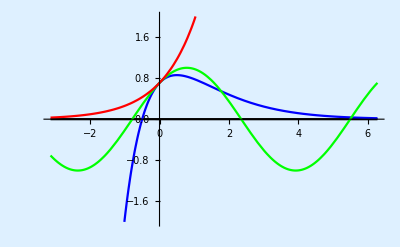
-Graphics-Universal oscillator equation with no external force

```mathematica
Framed[Labeled[Plot[Evaluate[({0, xP1,x[t, 0], xM1}/.{x0->1/√2, x1->1/√2})], {t, -π, 2π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["ζ == 1", 14], Style["ζ == 0", 14], Style["ζ == -1", 14]}, LegendPosition->{0.3,0.3}, LegendSize->{0.6,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Universal oscillator equation with no external force", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

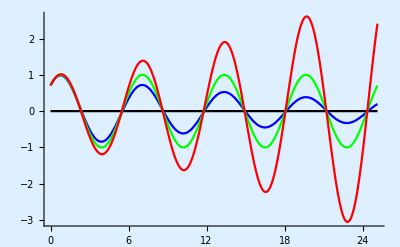
-Graphics-Universal oscillator equation with no external force

```mathematica
Framed[Labeled[Plot[Evaluate[({0, x[t, 0.05],x[t, 0], x[t, -0.05]}/.{x0->1/√2, x1->1/√2})], {t, 0, 8π}, PlotRange->All, PlotLegend->{Style["sin(t+π/2)", 14], Style["ζ == .05", 14], Style["ζ == 0", 14], Style["ζ == -.05", 14]}, LegendPosition->{-0.85,-0.6}, LegendSize->{0.6,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Universal oscillator equation with no external force", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

## Universal oscillator equation with external force

```mathematica
uoe = {δ->1, γ->2 ζ, β->1, α->0, a->1, ω->1};
```

```mathematica
x = Function[{t, ζ},(Evaluate[FullSimplify[numer//.reinsert//.uoe, ass]/FullSimplify[denom//.reinsert//.uoe, ass]])]
```

Function[{t,ζ},{-1/(4 ζ √(-1+ζ^2))ⅇ^(-t (ζ+√(-1+ζ^2))) (-2 x0 ζ √(-1+ζ^2)-2 ⅇ^(2 t √(-1+ζ^2)) x0 ζ √(-1+ζ^2)-√(-1+ζ^2) Cos[ϕ]-ⅇ^(2 t √(-1+ζ^2)) √(-1+ζ^2) Cos[ϕ]+2 ⅇ^(t (ζ+√(-1+ζ^2))) √(-1+ζ^2) Cos[t+ϕ]-(-1+ⅇ^(2 t √(-1+ζ^2))) (2 ζ (x1+x0 ζ)+ζ Cos[ϕ]-Sin[ϕ]))}]

```mathematica
xP1 = FullSimplify[Limit[x[t, ζ], ζ->1], ass]
```

{1/2 ⅇ^-t (2 (x0+t x0+t x1)+(1+t) Cos[ϕ]-ⅇ^t Cos[t+ϕ]-t Sin[ϕ])}

```mathematica
xM1 = FullSimplify[Limit[x[t, ζ], ζ->-1], ass]
```

{1/2 (Cos[t+ϕ]+ⅇ^t (2 (x0-t x0+t x1)+(-1+t) Cos[ϕ]+t Sin[ϕ]))}

```mathematica
x00 = FullSimplify[Limit[x[t, ζ], ζ->0], ass]
```

{x0 Cos[t]+1/2 (-t Cos[t+ϕ]+(2 x1+Cos[ϕ]) Sin[t])}

```mathematica
TrigExpand[x00]//TrigFactor
```

{1/4 (4 x0 Cos[t]-2 t Cos[t+ϕ]+4 x1 Sin[t]+Sin[t-ϕ]+Sin[t+ϕ])}

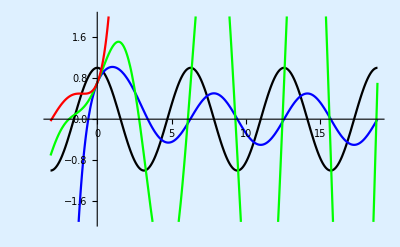
-Graphics-Universal oscillator equation with external force

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], xP1,x00, xM1}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["ζ == 1", 14], Style["ζ == 0", 14], Style["ζ == -1", 14]}, LegendPosition->{0.3,0.3}, LegendSize->{0.6,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Universal oscillator equation with external force", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

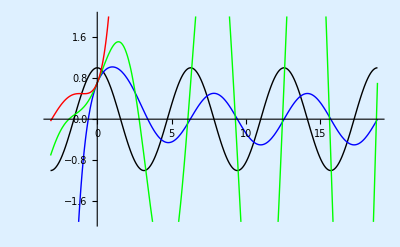

```mathematica
Plot[Evaluate[({Sin[t+ϕ], xP1,x00, xM1}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["Sin[t+π/2]", 14], Style["ζ == 1", 14]}, LegendPosition->{0.3,0.3}, LegendSize->{0.6,0.3},LegendShadow->{.02,-.02}]
```

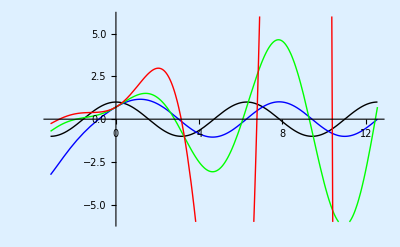

```mathematica
Plot[Evaluate[({Sin[t+ϕ], FullSimplify[Limit[x[t, ζ], ζ->1/2], ass],x00, FullSimplify[Limit[x[t, ζ], ζ->-1/2], ass]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 4π}, PlotRange->6]
```

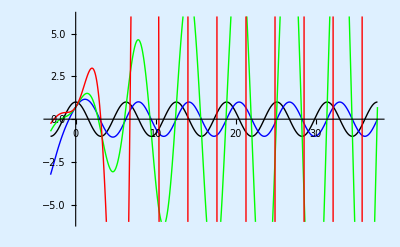

```mathematica
Plot[Evaluate[({Sin[t+ϕ], FullSimplify[Limit[x[t, ζ], ζ->1/2], ass],x00, FullSimplify[Limit[x[t, ζ], ζ->-1/2], ass]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 12π}, PlotRange->6]
```

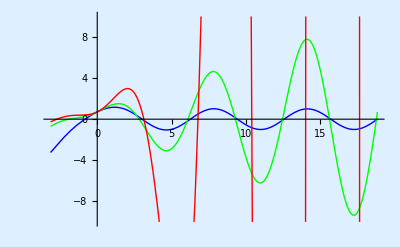

```mathematica
Plot[Evaluate[({FullSimplify[Limit[x[t, ζ], ζ->1/2], ass],FullSimplify[Limit[x[t, ζ], ζ->0], ass], FullSimplify[Limit[x[t, ζ], ζ->-1/2], ass]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->10, BaseStyle->Directive["Times", 16], Background->LightBlue, PlotStyle->{{Thick, Blue}, {Thick, Green}, {Thick, Red}, {Thick, Orange}}]
```

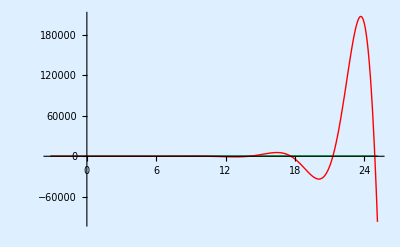

```mathematica
Plot[Evaluate[({FullSimplify[Limit[x[t, ζ], ζ->1/2], ass],FullSimplify[Limit[x[t, ζ], ζ->0], ass], FullSimplify[Limit[x[t, ζ], ζ->-1/2], ass]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 8π}, PlotRange->All, BaseStyle->Directive["Times", 16], Background->LightBlue, PlotStyle->{{Thick, Blue}, {Thick, Green}, {Thick, Red}, {Thick, Orange}}]
```

## Simple Pendulum no external force

Simple mathematical pendulum, no friction, no external force is applied.  The differential equation is only valid for small angles. l refers to the length of the pendulum and g to the gravitational accelartion.

```mathematica
smplPndlm = {δ->1, γ->0, β->g/l, α->0, a->0, ω->0};
assPndlm = Join[ass, {g>0, l>0}];
```

```mathematica
pndlm = Function[{t, g, l},(Evaluate[FullSimplify[FullSimplify[numer//.reinsert//.smplPndlm, assPndlm]/FullSimplify[denom//.reinsert//.smplPndlm, assPndlm], assPndlm]])]
```

Function[{t,g,l},{x0 Cos[√(g/l) t]+(l x1 Sin[√(g/l) t])/(√(g l))}]

If the pendulum is lifted to a height of 1 and then released it follows a sine wave.

```mathematica
pndlm[t, g, l]/.{x0->1, x1->0, ϕ->π/2}
```

{Cos[√(g/l) t]}

The time period depends only the length of the pendulum l and the gravitation constant g.

```mathematica
pos =First[Position[pndlm[t, g, l], Sin[_], ∞]];
FullSimplify[1/(pndlm[t, g, l][[Sequence@@Append[pos, 1]]]/(2 π t)), assPndlm]
```

2 √(l/g) π

In the plot below, the sinusoidal function is not visible, since it is covered by the blue line. Increasing the length of the pendulum by a factor four halves the frequency while decreasing the length of the pendulum to one quarter doubles the frequency.

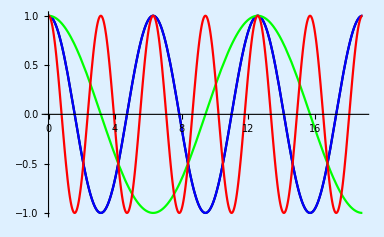
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | l = 1
▬▬▬  | l = 4
▬▬▬  | l = 1/4
no friction, no external forces | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], pndlm[t, 1,1], pndlm[t, 1,4], pndlm[t, 1,1/4]}/.{x0->1, x1->0, ϕ->π/2})], {t, 0, 6π}, PlotRange->Automatic, ImageSize->384]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "l = 1", "l = 4", "l = 1/4", "no friction, no external forces"]}, Frame->True]
```

## Simple Pendulum Undamped Sinusoidal Force

Simple mathematical Pendulum, no friction, but an sinusoidal external force is applied.  The differential equation is only valid for small angles. l refers to the length of the pendulum and g to the gravitational acceleration.

```mathematica
smplPndlmSF = {δ->1, γ->0, β->g/l, α->0};
assPndlmSF = Join[ass, {g>0, l>0, a>0}];
```

The function depends also on the amplitude of the sinusoidal force a and on the the frequency ω.

```mathematica
pndlmSF = Function[{t, g, l, a, ω},(Evaluate[FullSimplify[FullSimplify[numer//.reinsert//.smplPndlmSF, assPndlmSF]/FullSimplify[denom//.reinsert//.smplPndlmSF, assPndlmSF], assPndlmSF]])]
```

Function[{t,g,l,a,ω},{(√(g l) (g x1-l x1 ω^2-a l ω Cos[ϕ]) Sin[√(g/l) t]+g Cos[√(g/l) t] (x0 (g-l ω^2)-a l Sin[ϕ])+a g l Sin[ϕ+t ω])/(g (g-l ω^2))}]

The initial conditions assume that the mass of the pendulum is lifted to a height 1 and then released.

```mathematica
FullSimplify[pndlmSF[t, g, l, a, ω]/.{x0->1, x1->0, ϕ->π/2}, assPndlmSF]
```

{((g-l (a+ω^2)) Cos[√(g/l) t]+a l Cos[t ω])/(g-l ω^2)}

The external force is a sinus.  If the pendulum has the same frequency as the external force, the amplitude grows continuously, linearly with time.

```mathematica
FullSimplify[Limit[pndlmSF[t, 1, 1, 1,ω], ω->1]/.{x0->1, x1->0, ϕ->π/2}, assPndlmSF]
```

{Cos[t]+1/2 t Sin[t]}

If the frequency is smaller or larger but in phase, the pendulum’s movement deviates from a perfect sinus and becomes distorted.

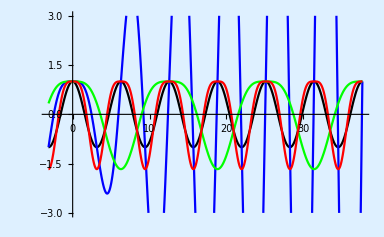
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | ω = 1
▬▬▬  | ω = 1/2
▬▬▬  | ω = 2
no friction, sinusoidal force
initially in phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmSF[t, 1,1, 1, ω],ω->1], pndlmSF[t, 1,1, 1, 1/2], pndlmSF[t, 1,1, 1, 2]}/.{x0->1, x1->0, ϕ->π/2})], {t, -π, 12π}, PlotRange->3, ImageSize->384]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "ω = 1", "ω = 1/2", "ω = 2", "no friction, sinusoidal force\ninitially in phase"]}, Frame->True]
```

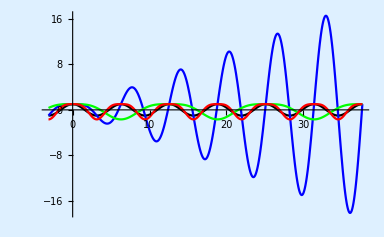
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | ω = 1
▬▬▬  | ω = 1/2
▬▬▬  | ω = 2
no friction, sinusoidal force
initially in phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmSF[t, 1,1, 1, ω],ω->1], pndlmSF[t, 1,1, 1, 1/2], pndlmSF[t, 1,1, 1, 2]}/.{x0->1, x1->0, ϕ->π/2})], {t, -π, 12π}, PlotRange->All, ImageSize->384]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "ω = 1", "ω = 1/2", "ω = 2", "no friction, sinusoidal force\ninitially in phase"]}, Frame->True]
```

## Simple Pendulum Damped Sinusoidal Force

Simple mathematical Pendulum, with friction and a sinusoidal external force is applied.  The differential equation is only valid for small angles. l refers to the length of the pendulum and g to the gravitational acceleration.

```mathematica
smplPndlmDSF = {δ->1, β->g/l, α->0};
assPndlmDSF = Join[ass, {g>0, l>0, γ>0}];
```

```mathematica
pndlmDSF = Function[{t, g, l, a, ω, γ},(Evaluate[FullSimplify[FullSimplify[numer//.reinsert//.smplPndlmDSF, assPndlmDSF]/FullSimplify[denom//.reinsert//.smplPndlmDSF, assPndlmDSF], assPndlmDSF]])]
```

Function[{t,g,l,a,ω,γ},{-((ⅇ^(-(t γ)/2) (-√(-(4 g)/l+γ^2) Cosh[1/2 t √(-(4 g)/l+γ^2)] (x0 (g^2-2 g l ω^2+l^2 ω^2 (γ^2+ω^2))+a l (-g Sin[ϕ]+l ω (γ Cos[ϕ]+ω Sin[ϕ])))+a ⅇ^((t γ)/2) √(l (-4 g+l γ^2)) (l γ ω Cos[ϕ+t ω]+(-g+l ω^2) Sin[ϕ+t ω])-((2 x1+x0 γ) (g^2-2 g l ω^2+l^2 ω^2 (γ^2+ω^2))+a l ω (-2 g+l (γ^2+2 ω^2)) Cos[ϕ]-a l γ (g+l ω^2) Sin[ϕ]) Sinh[1/2 t √(-(4 g)/l+γ^2)]))/(√(-(4 g)/l+γ^2) (g^2-2 g l ω^2+l^2 ω^2 (γ^2+ω^2))))}]

The initial conditions assume that the mass of the pendulum is lifted to a height 1 and then released.

```mathematica
FullSimplify[pndlmDSF[t, g, l, a, ω, γ]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF]
```

{-((ⅇ^(-(t γ)/2) (-√(-(4 g)/l+γ^2) (g^2+l^2 ω^2 (a+γ^2+ω^2)-g l (a+2 ω^2)) Cosh[1/2 t √(-(4 g)/l+γ^2)]-a ⅇ^((t γ)/2) √(l (-4 g+l γ^2)) ((g-l ω^2) Cos[t ω]+l γ ω Sin[t ω])-γ (g^2+l^2 ω^2 (-a+γ^2+ω^2)-g l (a+2 ω^2)) Sinh[1/2 t √(-(4 g)/l+γ^2)]))/(√(-(4 g)/l+γ^2) (g^2-2 g l ω^2+l^2 ω^2 (γ^2+ω^2))))}

The term ⅇ^(-t/2) is resposnible for damoing certain expressions.  Replacing it by zero allows us to determine the long term behaviour of the system.  The main effect is that a pure sinusoidal function develops that is undistorted.

```mathematica
expr=((FullSimplify[pndlmDSF[t, 1, 1, 1, ω, 1]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF]//Expand)/.ⅇ^(-t/2)->0)//TrigReduce//First
```

(Cos[t ω]-ω^2 Cos[t ω]+ω Sin[t ω])/(1-ω^2+ω^4)

```mathematica
Together[FullSimplify[FourierTransform[expr, t, Subscript[ω, 0]], { Subscript[ω, 0] > 0, ω>0}]]
```

-(√(π/2) DiracDelta[-ω+ω_0])/(-1+ⅈ ω+ω^2)

```mathematica
((FullSimplify[pndlmDSF[t, 1, 1, 1, 1, 1]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF]//Expand)/.ⅇ^(-t/2)->0)//TrigReduce
```

{Sin[t]}

Higher frequencies also return sinusoidal functions but with a smaller amplitude.

```mathematica
expr1 =((FullSimplify[pndlmDSF[t, 1, 1, 1, 2, 1]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF]//Expand)/.ⅇ^(-t/2)->0)//TrigReduce
```

{1/13 (-3 Cos[2 t]+2 Sin[2 t])}

```mathematica
sol1 = FindMinimum[-expr1, {t, 30.0}]
```

{-0.27735,{t→23.2679}}

```mathematica
3/13//N
```

0.230769

Lower frequencies also result in sinusoidal functions but have a slightly higher amplitude than initially and than the external sinusoidal force.  In the case below the amplitude is almost 11% larger.

```mathematica
expr2 = ((FullSimplify[pndlmDSF[t, 1, 1, 1, 1/2, 1]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF]//Expand)/.ⅇ^(-t/2)->0)//TrigReduce
```

{4/13 (3 Cos[t/2]+2 Sin[t/2])}

```mathematica
sol2 =FindMinimum[-expr2, {t, 14.0}]
```

{-1.1094,{t→13.7424}}

```mathematica
FourierCosSeries[First[expr2], t, 1]//N
```

0.979415+0.130589 Cos[t]

```mathematica
FourierCosSeries[First[expr2], t, 3]//N
```

0.979415+0.130589 Cos[t]-0.130589 Cos[2. t]+0.0111933 Cos[3. t]

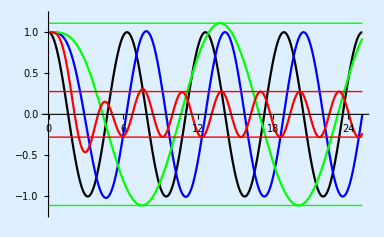
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | ω = 1
▬▬▬  | ω = 1/2
▬▬▬  | ω = 2
friction, sinusoidal force
initially in phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmDSF[t, 1,1, 1, ω, 1], ω->1], pndlmDSF[t, 1,1, 1, 1/2, 1], pndlmDSF[t, 1,1, 1, 2, 1]}/.{x0->1, x1->0, ϕ->π/2})], {t, 0, 8π}, PlotRange->1.2, ImageSize->384, Epilog->{Green, Line[{{0, sol2[[1]]}, {8 π, sol2[[1]]}}], Line[{{0, -sol2[[1]]}, {8 π, -sol2[[1]]}}], Red, Line[{{0, sol1[[1]]}, {8 π, sol1[[1]]}}], Line[{{0, -sol1[[1]]}, {8 π, -sol1[[1]]}}]}]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "ω = 1", "ω = 1/2", "ω = 2", "friction, sinusoidal force\ninitially in phase"]}, Frame->True]
```

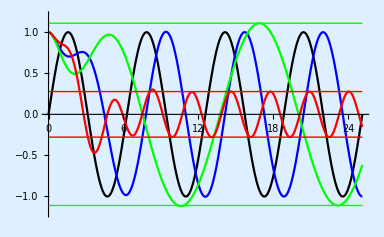
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | ω = 1
▬▬▬  | ω = 1/2
▬▬▬  | ω = 2
friction, sinusoidal force
initially out of phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmDSF[t, 1,1, 1, ω, 1], ω->1], pndlmDSF[t, 1,1, 1, 1/2, 1], pndlmDSF[t, 1,1, 1, 2, 1]}/.{x0->1, x1->0, ϕ->0})], {t, 0, 8π}, PlotRange->1.2, ImageSize->384, Epilog->{Green, Line[{{0, sol2[[1]]}, {8 π, sol2[[1]]}}], Line[{{0, -sol2[[1]]}, {8 π, -sol2[[1]]}}], Red, Line[{{0, sol1[[1]]}, {8 π, sol1[[1]]}}], Line[{{0, -sol1[[1]]}, {8 π, -sol1[[1]]}}]}]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "ω = 1", "ω = 1/2", "ω = 2", "friction, sinusoidal force\ninitially out of phase"]}, Frame->True]
```

The friction influences the amplitude but not the phase.

```mathematica
((FullSimplify[pndlmDSF[t, 1, 1, 1, 1, γ]/.{x0->1, x1->0, ϕ->π/2}, assPndlmDSF])//Expand)
```

{ⅇ^(-(t γ)/2) Cosh[1/2 t √(-4+γ^2)]+Sin[t]/γ-(2 ⅇ^(-(t γ)/2) Sinh[1/2 t √(-4+γ^2)])/(γ √(-4+γ^2))+(ⅇ^(-(t γ)/2) γ Sinh[1/2 t √(-4+γ^2)])/(√(-4+γ^2))}

```mathematica
%/.ⅇ^(-t γ/2)->0
```

{Sin[t]/γ}

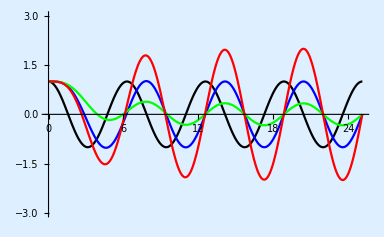
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | γ = 1
▬▬▬  | γ = 3
▬▬▬  | γ = 1/2
different frictions
sinusoidal force
initially in phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmDSF[t, 1,1, 1, ω, 1], ω->1], Limit[pndlmDSF[t, 1,1, 1, ω, 3], ω->1], Limit[pndlmDSF[t, 1,1, 1, ω, 1/2], ω->1]}/.{x0->1, x1->0, ϕ->π/2})], {t, 0, 8π}, PlotRange->3, ImageSize->384]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "γ = 1", "γ = 3", "γ = 1/2", "different frictions\nsinusoidal force\ninitially in phase"]}, Frame->True]
```

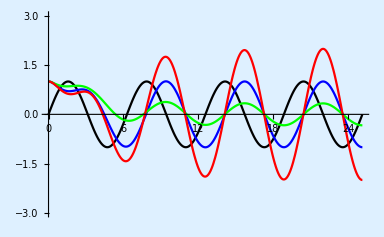
-Graphics-  ▬▬▬  | sin(t+π/2)
▬▬▬  | γ = 1
▬▬▬  | γ = 3
▬▬▬  | γ = 1/2
different frictions
sinusoidal force
initially out of phase | Simple Pendulum

```mathematica
Row[{Framed[Plot[Evaluate[({Sin[t+ϕ], Limit[pndlmDSF[t, 1,1, 1, ω, 1], ω->1], Limit[pndlmDSF[t, 1,1, 1, ω, 3], ω->1], Limit[pndlmDSF[t, 1,1, 1, ω, 1/2], ω->1]}/.{x0->1, x1->0, ϕ->0})], {t, 0, 8π}, PlotRange->3, ImageSize->384]],"  ",myLegend["Simple Pendulum", "sin(t+π/2)", "γ = 1", "γ = 3", "γ = 1/2", "different frictions\nsinusoidal force\ninitially out of phase"]}, Frame->True]
```

### Tasks

What happens when the amplitude of the external force is not identical to the inition condition?

What happens when the amplitude of the external force is modulated or simply changed?

What happens when the frequency of the external force is modulated?

## Series RLC with external constant source

```mathematica
SetOptions[Plot, {BaseStyle->Directive["Times", 16], Background->LightBlue, PlotStyle->{{Thick, Black}, {Thick, Blue}, {Thick, Green}, {Thick, Red}, {Thick, Orange}}}];
```

```mathematica
rlce = {δ->rL, γ->rR, β->(1/rC), α->0, a->1, ω->0};
rlceAss = Join[ass, {rL>0, rR>0, rC>0}];
```

```mathematica
q = Function[{t, rL, rR, rC},(Evaluate[FullSimplify[numer//.reinsert//.rlce, rlceAss]/FullSimplify[denom//.reinsert//.rlce, rlceAss]])]
```

Function[{t,rL,rR,rC},{1/(2 √(-4 rL+rC rR^2))ⅇ^(-((rR+√(-(4 rL)/rC+rR^2)) t)/(2 rL)) √rC (-rR x0+√(-(4 rL)/rC+rR^2) x0+ⅇ^((√(-(4 rL)/rC+rR^2) t)/rL) √(-(4 rL)/rC+rR^2) x0-2 rL x1+ⅇ^((√(-(4 rL)/rC+rR^2) t)/rL) (rR x0+2 rL x1)-rC ((-1+ⅇ^((√(-(4 rL)/rC+rR^2) t)/rL)) rR+(1+ⅇ^((√(-(4 rL)/rC+rR^2) t)/rL)-2 ⅇ^((rR t+√(-(4 rL)/rC+rR^2) t)/(2 rL))) √(-(4 rL)/rC+rR^2)) Sin[ϕ])}]

```mathematica
rlceUndamped = FullSimplify[Limit[q[t, rL, rR, rC], rR->0], rlceAss]
```

{√(rC rL) x1 Sin[t/(√(rC rL))]+rC Sin[ϕ]+Cos[t/(√(rC rL))] (x0-rC Sin[ϕ])}

```mathematica
pos =First[Position[rlceUndamped, Sin[_], ∞]];
FullSimplify[1/(rlceUndamped[[Sequence@@Append[pos, 1]]]/(2 π t)), rlceAss]
```

2 π √(rC rL)

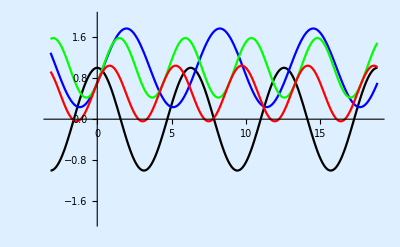
-Graphics-Series RLC with external constant source, R = 0

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 0, 1],q[t, 1/2, 0, 1], q[t, 1, 0, 1/2]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external constant source, R = 0", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 0, 1],q[t, 1/2, 0, 1], q[t, 1, 0, 1/2]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external constant source, R = 0", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

-Graphics-Series RLC with external constant source, R = 0

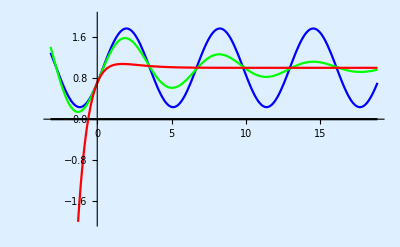
-Graphics-Series RLC with external constant source

```mathematica
Framed[Labeled[Plot[Evaluate[({0, q[t, 1, 0, 1],q[t, 1, 1/4, 1], Limit[q[t, 1, rR, 1], rR->2]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1,R=0,C=1", 14], Style["L=1,R=1/4,C=1", 14], Style["L=1,R=2,C=1", 14]}, LegendPosition->{0.0,-0.55}, LegendSize->{0.95,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external constant source", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

## Series RLC with external oscillating source

```mathematica
SetOptions[Plot, {BaseStyle->Directive["Times", 16], Background->LightBlue, PlotStyle->{{Thick, Black}, {Thick, Blue}, {Thick, Green}, {Thick, Red}, {Thick, Orange}}}];
```

```mathematica
rlco = {δ->rL, γ->rR, β->(1/rC), α->0};
rlcoAss = Join[ass, {rL>0, rR>0, rC>0}];
```

```mathematica
q = Function[{t, rL, rR, rC, a, ω},(Evaluate[FullSimplify[numer//.reinsert//.rlco, rlcoAss]/FullSimplify[denom//.reinsert//.rlco, rlcoAss]])]
```

Function[{t,rL,rR,rC,a,ω},{-((ⅇ^(-(rR t)/(2 rL)) (-√(-(4 rL)/rC+rR^2) Cosh[(√(-(4 rL)/rC+rR^2) t)/(2 rL)] (x0+rC (-2 rL+rC rR^2) x0 ω^2+rC^2 rL^2 x0 ω^4+a rC (rC rR ω Cos[ϕ]+(-1+rC rL ω^2) Sin[ϕ]))+a ⅇ^((rR t)/(2 rL)) √(rC (-4 rL+rC rR^2)) (rC rR ω Cos[ϕ+t ω]+(-1+rC rL ω^2) Sin[ϕ+t ω])-((rR x0+2 rL x1) (1+rC ω^2 (rC rR^2+rL (-2+rC rL ω^2)))+a rC ω (rC rR^2+2 rL (-1+rC rL ω^2)) Cos[ϕ]-a rC rR (1+rC rL ω^2) Sin[ϕ]) Sinh[(√(-(4 rL)/rC+rR^2) t)/(2 rL)]))/(√(-(4 rL)/rC+rR^2) (1+rC ω^2 (rC rR^2+rL (-2+rC rL ω^2)))))}]

```mathematica
rlcoUndamped = FullSimplify[Limit[q[t, rL, rR, rC, ω, a], rR->0], rlcoAss]
```

{(√(rC rL) (-x1+a^2 rC rL x1+a rC ω Cos[ϕ]) Sin[t/(√(rC rL))]+Cos[t/(√(rC rL))] ((-1+a^2 rC rL) x0+rC ω Sin[ϕ])-rC ω Sin[a t+ϕ])/(-1+a^2 rC rL)}

```mathematica
pos =First[Position[rlcoUndamped, Sin[_], ∞]];
FullSimplify[1/(rlcoUndamped[[Sequence@@Append[pos, 1]]]/(2 π t)), rlcoAss]
```

2 π √(rC rL)

```mathematica
TrigExpand[FullSimplify[q[t, 1, 1, 1, 1, 1]/.{x0->1, x1->0, ϕ->π/2}]]
```

{ⅇ^(-t/2) Cos[(√3 t)/2]+Sin[t]-(ⅇ^(-t/2) Sin[(√3 t)/2])/(√3)}

```mathematica
%/.ⅇ^(-t/2)->0
```

{Sin[t]}

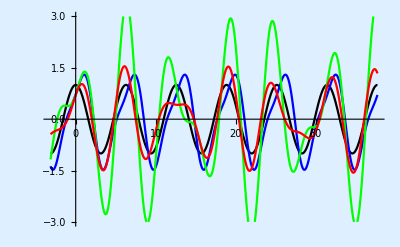
-Graphics-Series RLC with external oscillator source, R = 0, ω=a=1

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 0, 1,1,2],q[t, 1/2, 0, 1,1,1], q[t, 1, 0, 1/2,1,1]}/.{x0->1/√2, x1->1/√2, ϕ->π/2})], {t, -π, 12π}, PlotRange->3, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external oscillator source, R = 0, ω=a=1", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

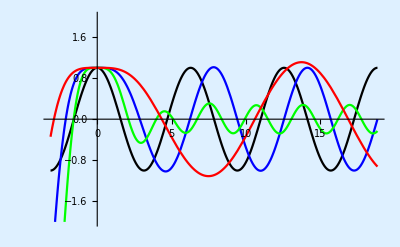
-Graphics-Series RLC with external oscillating source

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 1, 1, 1, 1],q[t, 1, 1, 1, 1, 2], q[t, 1, 1, 1, 1, 1/2]}/.{x0->1, x1->0, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external oscillating source", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

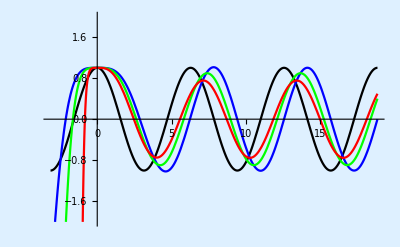
-Graphics-Series RLC with external oscillating source

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 1, 1, 1, 1],q[t, 1/2, 1, 1, 1, 1], q[t, 1/8, 1, 1, 1, 1]}/.{x0->1, x1->0, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external oscillating source", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

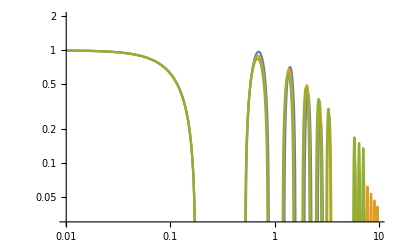

```mathematica
LogLogPlot[Evaluate[({q[10, 1/2, 1, 1, 1,ω],Limit[q[10, rL, 1, 1, 1, ω], rL->1/4], q[10, 1/16, 1, 1, 1, ω]}/.{x0->1, x1->0, ϕ->π/2})], {ω, 0.01, 10.0}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{-0.8,-0.45}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray]
```

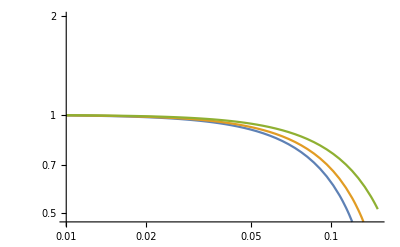

```mathematica
LogLogPlot[Evaluate[({q[10, 1/2, 1, 1, 1,ω],Limit[q[10, rL, 2, 1, 1, ω], rL->1/4], q[10, 1/16, 4, 1, 1, ω]}/.{x0->1, x1->0, ϕ->π/2})], {ω, 0.01, 0.15}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{-0.8,-0.45}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray]
```

```mathematica
Framed[Labeled[Plot[Evaluate[({Sin[t+ϕ], q[t, 1, 1, 1, 1, 1],q[t, 1/2, 1, 1, 1, 1], q[t, 1/8, 1, 1, 1, 1]}/.{x0->1, x1->0, ϕ->π/2})], {t, -π, 6π}, PlotRange->2, PlotLegend->{Style["sin(t+π/2)", 14], Style["L=1, C=1", 14], Style["L=1/2, C=1", 14], Style["L=1, C=1/2", 14]}, LegendPosition->{0.2,-0.58}, LegendSize->{0.66,0.33},LegendShadow->{.02,-.02}, LegendBackground->LightGray], Style["Series RLC with external oscillating source", FontFamily->"Times", 16, Black], Top, Frame->True], Background->LightGray]
```

-Graphics-Series RLC with external oscillating source